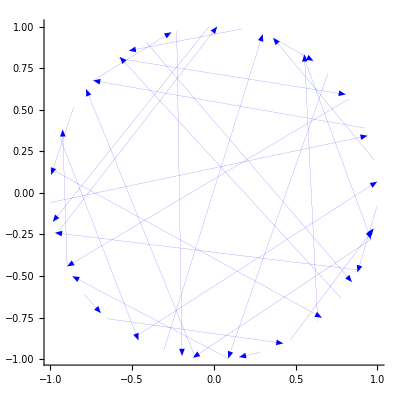

-b Cos[t]+b Cos[6 t]+a Sin[t]+Sin[5 t]-a Sin[6 t]

a Cos[t]+5 Cos[5 t]-6 a Cos[6 t]+b Sin[t]-6 b Sin[6 t]

```mathematica
ClearAll["Global`*"];
i=6;
P1[t_]:=(x=Cos[t];y=Sin[t];{x,y});
P2[t_]:=(x=Cos[i*t];y=Sin[i*t];{x,y});
lines=Table[{P1[t],P2[t]},{t,0*2Pi,1*2Pi,0.2}];
Graphics[{Blue, Thickness[0.0001],Map[Arrow,lines],PlotRange->{{-1,1},{-1,1}},AspectRatio->1},Axes->True]
(* Using equation 16, the two-point form, we obtain the system of equations *)
F[x_,y_,t_]:=(y-P1[t][[2]])(P2[t][[1]]-P1[t][[1]])-(x-P1[t][[1]])(P2[t][[2]]-P1[t][[2]]);
Print[FullSimplify[F[a,b,t]]];
Print[FullSimplify[D[F[a,b,t],t]]];
```

{{u→-(5 Cos[t] Cos[5 t]-5 Cos[5 t] Cos[6 t]+Sin[t] Sin[5 t]-6 Sin[5 t] Sin[6 t])/(Cos[t]^2-7 Cos[t] Cos[6 t]+6 Cos[6 t]^2+Sin[t]^2-7 Sin[t] Sin[6 t]+6 Sin[6 t]^2),v→-(5 Cos[5 t] Sin[t]-Cos[t] Sin[5 t]+6 Cos[6 t] Sin[5 t]-5 Cos[5 t] Sin[6 t])/(Cos[t]^2-7 Cos[t] Cos[6 t]+6 Cos[6 t]^2+Sin[t]^2-7 Sin[t] Sin[6 t]+6 Sin[6 t]^2)}}

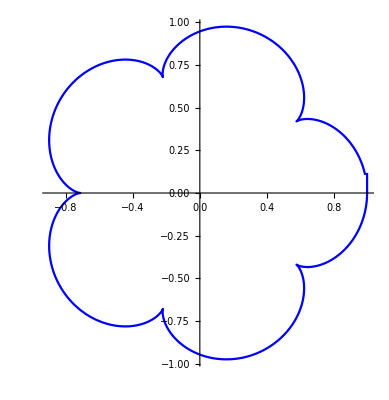

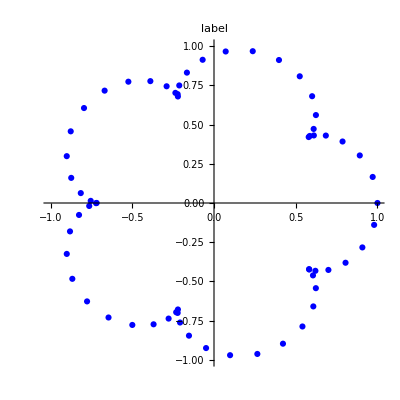

```mathematica
ClearAll["Global`*"];
i=6;
F[x_,y_,t_]:=-y Cos[t]+y Cos[i t]+x Sin[t]-x Sin[i t]-Sin[t-i t];
Fd[x_,y_,t_]:=x Cos[t]-x i Cos[i t]+(-1+i) Cos[t-i t]+y Sin[t]-y i Sin[i t];
(* Retrieve the intersection Points P[u(t),v(t)] *)
Print[Solve[F[u,v,t]==0&&Fd[u,v,t]==0,{u,v}]];
parametricFunc[t_]:={u,v}/.(Solve[F[u,v,t]==0&&Fd[u,v,t]==0,{u,v}]);
ParametricPlot[parametricFunc[t],{t,0.01*2Pi,1*2Pi},PlotStyle->Blue]
(* Full simplifying u(t) and v(t) brings us to this compact form *)
P[t_]=(x=(i Cos[t]+Cos[i t])/(1+i);y=(i Sin[t]+Sin[i t])/(1+i);{x,y});
ListPlot[Table[P[t],{t,0*2Pi,1*2Pi,0.1}],PlotRange->{{-1,1},{-1,1}},AspectRatio->1, PlotLabel->label,PlotStyle->Blue]
```